```mathematica
myfile=Import["Directroy\\FileName"];
```

```mathematica
(*The list order in Excel file: Hoechst, Alexa488, Cy3, Cy5*)

PreList=Table[myfile[[1,1;;All,i]]//Take[#,450]&,{i,1,4,1}];
(*Division by average*)
NorList=Table[Table[PreList⟦j⟧⟦i⟧/(Mean[PreList⟦j⟧]),{i, 1,Length[PreList⟦j⟧],1}]//Flatten,{j,1,4,1}];
```

## Figure 1D,1E

```mathematica
(*Normalization*)
HoechstList=Table[{(NorList⟦1⟧⟦i⟧-RankedMin[NorList⟦1⟧,5])/(RankedMax[NorList⟦1⟧,5]-RankedMin[NorList⟦1⟧,5])+1},{i,1,Length[NorList⟦1⟧],1}]//Flatten;
Cy5List=Table[{(NorList⟦4⟧⟦i⟧-RankedMin[NorList⟦4⟧,5])/(RankedMax[NorList⟦4⟧,5]-RankedMin[NorList⟦4⟧,5])},{i,1,Length[NorList⟦4⟧],1}]//Flatten;
```

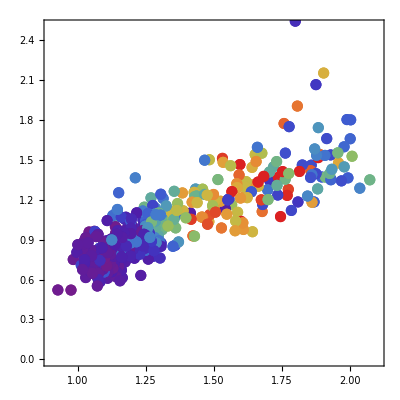

```mathematica
StyleList=Table[{PointSize[0.02],ColorData["Rainbow"]
[(Cy5List⟦i⟧-Min[Cy5List])/(RankedMax[Cy5List,10]-Min[Cy5List])]},{i,1,Length[Cy5List],1}];
{{HoechstList,NorList⟦2⟧}//Transpose}//Transpose//ListPlot[#,PlotStyle->StyleList,
Frame->True,AxesOrigin->{0,0},AspectRatio->1,PlotRange->{{0.9,2.1}, {0,2.5}}]&
```

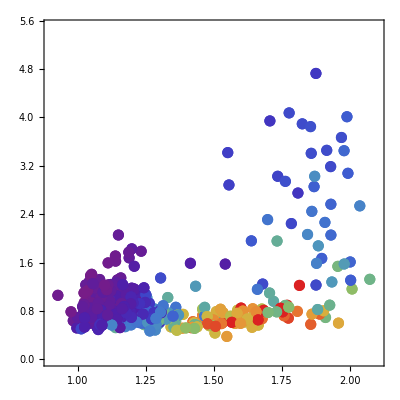

```mathematica
StyleList=Table[{PointSize[0.02],ColorData["Rainbow"]
[(Cy5List⟦i⟧-Min[Cy5List])/(RankedMax[Cy5List,10]-Min[Cy5List])]},{i,1,Length[Cy5List],1}];
{{HoechstList,NorList⟦3⟧}//Transpose}//Transpose//ListPlot[#,PlotStyle->StyleList,
Frame->True,AxesOrigin->{0,0},AspectRatio->1,PlotRange->{{0.9,2.1}, {0,5.5}}]&
```

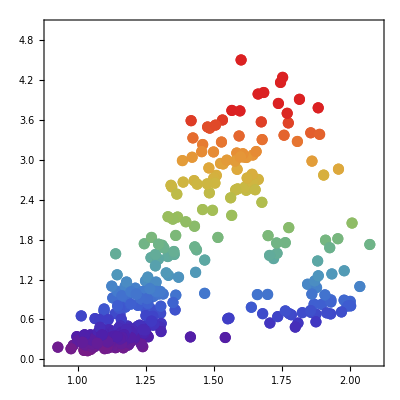

```mathematica
StyleList=Table[{PointSize[0.02],ColorData["Rainbow"]
[(Cy5List⟦i⟧-Min[Cy5List])/(RankedMax[Cy5List,10]-Min[Cy5List])]},{i,1,Length[Cy5List],1}];
{{HoechstList,NorList⟦4⟧}//Transpose}//Transpose//ListPlot[#,PlotStyle->StyleList,
Frame->True,AxesOrigin->{0,0},AspectRatio->1,PlotRange->{{0.9,2.1}, {0,5}}]&
```

## Figure 1F

```mathematica
(*Sort by hoechst*)
SortList=Table[NorList⟦i⟧⟦Ordering[NorList⟦1⟧]⟧,{i,1,4,1}];
```

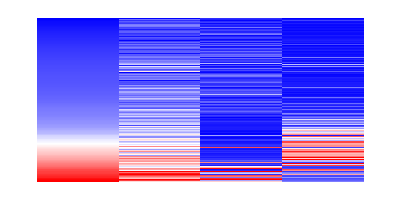

```mathematica
ArrayPlot[{(SortList⟦1⟧-RankedMin[SortList⟦1⟧,5])/(RankedMax[SortList⟦1⟧,5]-RankedMin[SortList⟦1⟧,5]),(SortList⟦2⟧-RankedMin[SortList⟦2⟧,5])/(RankedMax[SortList⟦2⟧,5]-RankedMin[SortList⟦2⟧,5]),(SortList⟦3⟧-RankedMin[SortList⟦3⟧,5])/(RankedMax[SortList⟦3⟧,5]-RankedMin[SortList⟦3⟧,5]),(SortList⟦4⟧-RankedMin[SortList⟦4⟧,5])/(RankedMax[SortList⟦4⟧,5]-RankedMin[SortList⟦4⟧,5])}//Transpose,AspectRatio->1/2,ColorFunctionScaling->False,ColorFunction->Function[{z}, RGBColor[If[z<0.5,2z,1],If[z<0.5, 2z, 2(1-z)],If[z<0.5,1,2(1-z)] ]],PlotRange->{All,All,All},Frame->False,Frame->False]
```